```mathematica
Clear["Global`*"]
```

```mathematica
Get["/home/viktor/Dropbox/projects/anyons/thesis/code/fibonacci_Up.wl"];
```

(Rτ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | R1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Rτ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | B11 | B12 | 0 | 0 | 0
0 | 0 | 0 | B21 | B22 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | B11 | 0 | B12
0 | 0 | 0 | 0 | 0 | 0 | Rτ | 0
0 | 0 | 0 | 0 | 0 | B21 | 0 | B22)

True

eigenvalues with mult.:
ⅇ^((ⅈ π)/5) × 4, ⅇ^((4 ⅈ π)/5) × 8, ⅇ^(-(3 ⅈ π)/5) × 3, ⅇ^(-(ⅈ π)/5) × 6,

det(Uₚ) = ⅇ^((ⅈ π)/5)

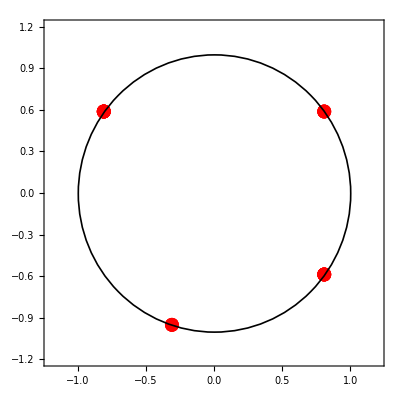

(<|-3/5→3,-1/5→3,1/5→2,4/5→5|>
<|-3/5→3,-1/5→6,1/5→4,4/5→8|>
<|-3/5→6,-1/5→9,1/5→6,4/5→13|>)

```mathematica
Get["/home/viktor/Dropbox/projects/anyons/thesis/code/fibonacci_eigenvalues.wl"];
```

```mathematica
Get["/home/viktor/Dropbox/projects/anyons/thesis/fibonacci_fusedbasis.wl"];
```

(R1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Rτ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Rτ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Rτ^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | B11 | B12 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | B21 | B22 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | B11 R1^2 | B12 R1 Rτ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | B21 R1 Rτ | B22 Rτ^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | B11^2 R1+B12 B21 Rτ | B11 B12 R1+B12 B22 Rτ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | B11 B21 R1+B21 B22 Rτ | B12 B21 R1+B22^2 Rτ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | B12 B21 B22+B11^2 Rτ | B12 B21 Rτ | B12 B22^2+B11 B12 Rτ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | B12 B21 Rτ | B11 Rτ^2 | B12 B22 Rτ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | B21 B22^2+B11 B21 Rτ | B21 B22 Rτ | B22^3+B12 B21 Rτ)

```mathematica
Map[EigenvaluesArg[U[#]]&,{0,1,2}]
```

{{-3/5,-3/5,-3/5,4/5,4/5},{-1/5,-1/5,-1/5,1/5,1/5,4/5,4/5,4/5},{-3/5,-3/5,-3/5,-1/5,-1/5,-1/5,1/5,1/5,4/5,4/5,4/5,4/5,4/5}}

```mathematica
R=({{R1,0},{0,Rτ}});
B={{B11,B12},{B21,B22}};
B.R.B//MatrixForm
```

(B11^2 R1+B12 B21 Rτ | B11 B12 R1+B12 B22 Rτ
B11 B21 R1+B21 B22 Rτ | B12 B21 R1+B22^2 Rτ)

```mathematica
{{B11,0,B12},{0,Rτ,0},{B21,0,B22}}.{{Rτ,0,0},{0,B11,B12},{0,B21,B22}}.{{B11,0,B12},{0,Rτ,0},{B21,0,B22}}//MatrixForm
```

(B12 B21 B22+B11^2 Rτ | B12 B21 Rτ | B12 B22^2+B11 B12 Rτ
B12 B21 Rτ | B11 Rτ^2 | B12 B22 Rτ
B21 B22^2+B11 B21 Rτ | B21 B22 Rτ | B22^3+B12 B21 Rτ)